### 2018/05/14 data (ventiles)

```mathematica
ventileData[ventile_]:=Module[{data,fName,dateStr,inDir,MLTString,keeps},
inDir="/SPENCEdata/Research/Satellites/FAST/kappa_dists/txtOutput/";
dateStr="20180514-";
MLTString="20_50-1_50MLT-";
fName=dateStr<>MLTString<>"goverkVentiles"<>ToString[ventile]<>"-allALT-NORTH-GoverK0_0-Kchi2Max0_0-allObs-normed.csv";
data=Import[inDir<>fName];
keeps=Position[data[[;;,2]],val_ /; val>0.1]//Flatten;
data=data[[keeps,;;]]
]
```

Define the fit function

```mathematica
Options[fitPackage]={fitAboveKappa->2.5,fitBelowKappa->Null,Quiet->False,PrintVals->False,IncludePlot->False};
```

```mathematica
fitPackage[data_,fitFunc_,fitParms_,parmConstr_:Null,OptionsPattern[]]:=
Module[{parmVals,fitDat,lowInd,highInd,twoPlots},

(*Cut off data at low end*)
lowInd=(Position[data[[;;,1]],Min[Select[data[[;;,1]],#≥ OptionValue[fitAboveKappa]&]]]//Flatten)[[1]];
fitDat=data[[lowInd;;,;;]];

(*Cut off data at high end?*)
If[OptionValue[fitBelowKappa]≠Null,
highInd=(Position[fitDat[[;;,1]],Min[Select[fitDat[[;;,1]],#≥ OptionValue[fitBelowKappa]&]]]//Flatten)[[1]];
fitDat=fitDat[[highInd;;,;;]];
];

If[!OptionValue[Quiet],
Print[StringForm["Function: `1`",fitFunc]];
Print[StringForm["Constraints: `1`",ToString@parmConstr]];
];

(*Print[ToString[Head[parmConstr]]];*)
If[(ToString[Head[parmConstr]]==ToString[List]),
parmVals = FindFit[fitDat,{fitFunc,Evaluate[parmConstr]},fitParms,x];,
parmVals = FindFit[fitDat,fitFunc,fitParms,x];
];

If[OptionValue[PrintVals],
Print[": Begin"];
Print[StringForm["a = `1`",NumberForm[a/.parmVals,6]]];
Print[StringForm["b = `1`",NumberForm[b/.parmVals,6]]];
Print[StringForm["c = `1`",NumberForm[c/.parmVals,6]]];
Print["End"];
];

If[OptionValue[IncludePlot],
twoPlots=Show[Plot[(fitFunc)/.parmVals,{x,1.6,80},PlotRange->{{1.5,30},{0.9,3.0}}],ListPlot[data]];
{parmVals,twoPlots},
parmVals
]
]
```

```mathematica
fitFunc=(a x +b)^c+1;
fitParms={a,b,c};
parmConstr={-10<=c<-1,a>0};
```

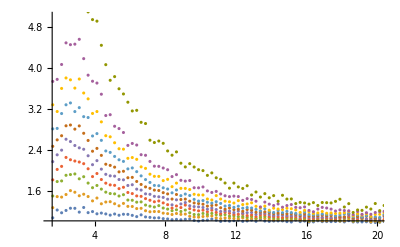

```mathematica
ListPlot[ventileData[#]&/@Range[0,18,2],PlotRange->{{1.5,20},{1,5}}]
```

```mathematica
parmVals=Table[fitPackage[ventileData[ventile],fitFunc,fitParms,parmConstr,fitBelowKappa->2.5,Quiet->True,PrintVals->True],{ventile,0,18}];
```

```mathematica
parmVals[[1]]
```

{a→0.0321162,b→1.05356,c→-9.99884}

```mathematica
Values@parmVals[[ventile]]
```

{0.0259515,0.954985,-9.99822}

a = 0.02595, b = 0.955, c = -9.998

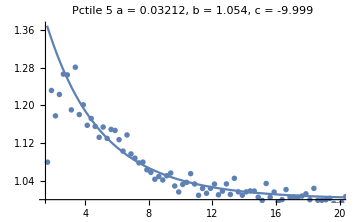
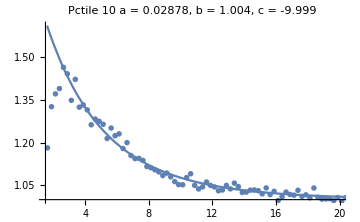
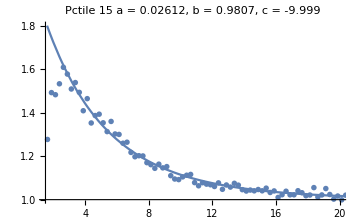
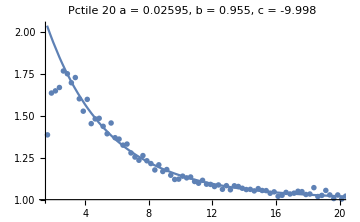
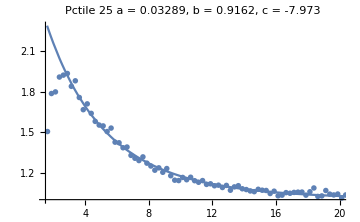
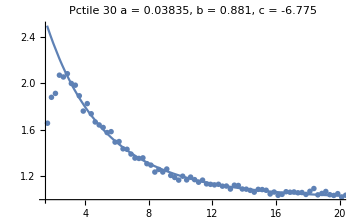
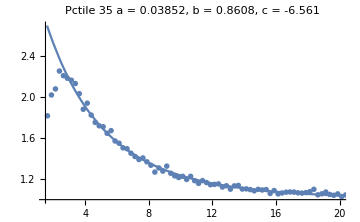
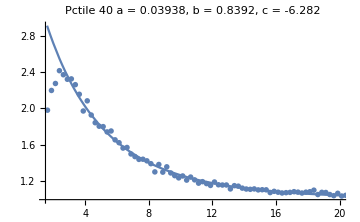

```mathematica
Table[Show[Plot[(fitFunc)/.parmVals[[ventile+1]],{x,1.6,80},PlotRange->{{1.5,20},Full},ImageSize->Medium,PlotLabel->TableForm[{{"Pctile "<>ToString[(ventile+1)*5]},
{StringForm["a = `1`, b = `2`, c = `3`",#1,#2,#3]&@@(NumberForm[#,4]&/@Values@parmVals[[ventile+1]])}}]],ListPlot[ventileData[ventile]]],{ventile,0,18}]
```